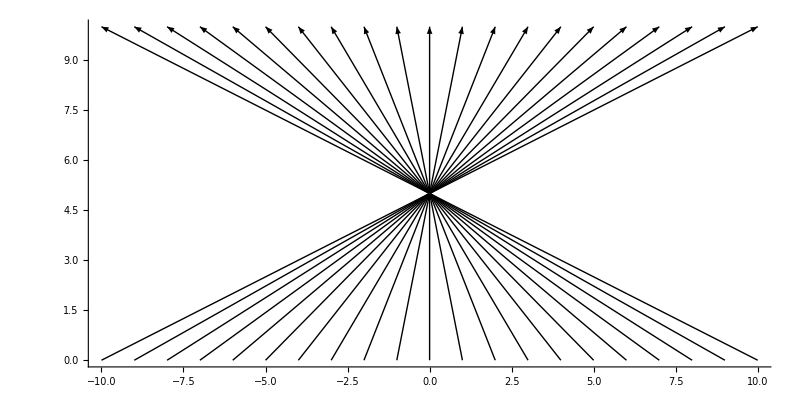

```mathematica
links = -10;
rechts = 10;
a=0.5;
vx[x_]:=-a (x-links) +a (rechts - x);
Graphics[
Map[
Arrow[#1]&,
Table[
{{x,0},{vx[x],10}},
{x,links,rechts,1}
]
],
Axes->True
]
```